# Decays

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/matheushostert/Repos/solar-neutrino-visible-decays/mathematica

```mathematica
Remove["Global`*"]
dm[mu_]:=DiracMatrix[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
```

```mathematica
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
```

```mathematica
Lambda[a_,b_,c_]:=(a-b-c)^2-4b c
```

## N -> nu Z’

```mathematica
k1CM = √(((Mn^2-Mzprime^2)/(2 Mn))^2);
ScalarProduct[P,P] = Mn^2;
ScalarProduct[P1,P1] = 0.0;
ScalarProduct[P2,P2] = Mzprime^2;
ScalarProduct[P1,P2] = (Mn^2-Mzprime^2)/2;
ScalarProduct[P,P2] = (Mn^2+Mzprime^2)/2;
ScalarProduct[P,P1] = (Mn^2-Mzprime^2)/2;
ScalarProduct[s,s]= -1;
ScalarProduct[s,P]=0;
ScalarProduct[s,P1]=-k1CM cosTheta;
ScalarProduct[s,P2]= k1CM cosTheta;
```

```mathematica
PolarizationSum[μ,μC ,P2]
```

(OverBar[P2]^μ OverBar[P2]^μC)/Mzprime^2-(ḡ)^μμC

```mathematica
m1 =  SpinorUBar[P1,0.0].(dm[μ].((1-dm[5])/2) .((1+ h dm[5].ds[s])/2)).SpinorU[P,Mn]
m1C =  SpinorUBar[P,Mn].(((1+ h dm[5].ds[s])/2).dm[μC].((1-dm[5])/2) ).SpinorU[P1,0.0]
M2 = Chop[FermionSpinSum[m1C*m1]].PolarizationSum[μ,μC ,P2]//Contract
Amp2=M2/.DiracTrace->Tr/.Pair[Momentum[P2],Momentum[P2]]-> Mzprime^2
```

ū(P1,0.).(γ̄)^μ.(1/2 (1-(γ̄)^5)).(1/2 (h (γ̄)^5.(γ̄·s̄)+1)).u(P,Mn)

ū(P,Mn).(1/2 (h (γ̄)^5.(γ̄·s̄)+1)).(γ̄)^μC.(1/2 (1-(γ̄)^5)).u(P1,0.)

(tr((γ̄·P̄+Mn).(h (γ̄)^5.(γ̄·s̄)+1).(γ̄·OverBar[P2]).(1-(γ̄)^5).(γ̄·OverBar[P1]).(γ̄·OverBar[P2]).(1-(γ̄)^5).(h (γ̄)^5.(γ̄·s̄)+1)))/(16 Mzprime^2)-1/16 tr((γ̄·P̄+Mn).(h (γ̄)^5.(γ̄·s̄)+1).(γ̄)^μC.(1-(γ̄)^5).(γ̄·OverBar[P1]).(γ̄)^μC.(1-(γ̄)^5).(h (γ̄)^5.(γ̄·s̄)+1))

1/2 (2 cosTheta h Mn √(((Mn^2-Mzprime^2)^2)/Mn^2)+h^2 Mn^2-h^2 Mzprime^2+Mn^2-Mzprime^2)-(Mn^2 (2 cosTheta h Mn √(((Mn^2-Mzprime^2)^2)/Mn^2)-h^2 Mn^2+h^2 Mzprime^2-Mn^2+Mzprime^2))/(4 Mzprime^2)

```mathematica
Amp2/.{h^2-> 1}//Simplify//PowerExpand//Simplify
```

((Mn^2-Mzprime^2) (Mn^2 (cosTheta h+1)-2 Mzprime^2 (cosTheta h-1)))/(2 Mzprime^2)

### Majorana case

```mathematica
m1M=  SpinorUBar[P1,0.0].(dm[μ].((1+ h dm[5].ds[s])/2)).SpinorU[P,Mn]
m1CM =  SpinorUBar[P,Mn].(((1+ h dm[5].ds[s])/2).dm[μC] ).SpinorU[P1,0.0]
M2M = Chop[FermionSpinSum[m1CD*m1D]].PolarizationSum[μ,μC ,P2]//Contract
Amp2M=M2M/.DiracTrace->Tr/.Pair[Momentum[P2],Momentum[P2]]-> Mzprime^2
```

ū(P1,0.).(γ̄)^μ.(1/2 (h (γ̄)^5.(γ̄·s̄)+1)).u(P,Mn)

ū(P,Mn).(1/2 (h (γ̄)^5.(γ̄·s̄)+1)).(γ̄)^μC.u(P1,0.)

(tr((γ̄·P̄+Mn).(h (γ̄)^5.(γ̄·s̄)+1).(γ̄·OverBar[P2]).(γ̄·OverBar[P1]).(γ̄·OverBar[P2]).(h (γ̄)^5.(γ̄·s̄)+1)))/(4 Mzprime^2)-1/4 tr((γ̄·P̄+Mn).(h (γ̄)^5.(γ̄·s̄)+1).(γ̄)^μC.(γ̄·OverBar[P1]).(γ̄)^μC.(h (γ̄)^5.(γ̄·s̄)+1))

(h^2+1) (Mn-Mzprime) (Mn+Mzprime)-((h^2+1) Mn^2 (Mzprime-Mn) (Mn+Mzprime))/(2 Mzprime^2)

```mathematica
Amp2M/.{h^2-> 1}//Simplify//PowerExpand//Simplify
```

Mn^4/Mzprime^2+Mn^2-2 Mzprime^2

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=pow[a,n]
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
Amp2/.{Mzprime-> r Mn,h^2-> 1}//PowerExpand//FullSimplify
```

-(Mn^2 (r^2-1) (2 r^2 (cosTheta h+1)-cosTheta h+1))/(2 r^2)

```mathematica
my= Mn^2/(2 r^2)(1-r^2)(1+h +(1-h)2r^2 - 2h re (1-2r^2)/(1-r^2))
```

(Mn^2 (1-r^2) (-(2 h (1-2 r^2) re)/(1-r^2)+2 (1-h) r^2+h+1))/(2 r^2)

```mathematica
myAMP2=Amp2/.{Mzprime-> r Mn}/.{cosTheta-> (2 E1)/(Enu(1-r^2))-1}/.{E1-> Enu re }/.h^2-> 1//PowerExpand//ExpandAll//FullSimplify
```

(Mn^2 (h (2 r^2-1) (r^2+2 re-1)-2 r^4+r^2+1))/(2 r^2)

```mathematica
myAMP2/.{h->-1}//FullSimplify
myAMP2/.{h-> 1}//FullSimplify
```

(Mn^2 (re-2 r^2 (r^2+re-1)))/r^2

(Mn^2 (r^2 (2 re-1)-re+1))/r^2

```mathematica
ratio = (Amp2 /.{h-> -1})/(Amp2 /.{h-> 1})/.{Mn-> Mzprime/r}//FullSimplify//PowerExpand//Simplify
```

(2 cosTheta r^2-cosTheta+2 r^2+1)/(-2 cosTheta r^2+cosTheta+2 r^2+1)

```mathematica
ratio/.{cosTheta-> 1}
ratio/.{cosTheta-> -1}
```

2 r^2

1/(2 r^2)

```mathematica
CForm[Amp2]/.{Mzprime-> mzprime,Mn-> mh,cosTheta-> CosTheta}
```

(mh*mh + h*h*(mh*mh) - mzprime*mzprime - h*h*(mzprime*mzprime) + 
      2*CosTheta*h*mh*Sqrt(((mh*mh - mzprime*mzprime)*(mh*mh - mzprime*mzprime))/(mh*mh)))/2. - 
   (mh*mh*(-(mh*mh) - h*h*(mh*mh) + mzprime*mzprime + h*h*(mzprime*mzprime) + 
        2*CosTheta*h*mh*Sqrt(((mh*mh - mzprime*mzprime)*(mh*mh - mzprime*mzprime))/(mh*mh))))/
    (4.*(mzprime*mzprime))

```mathematica
dPS2 = (√Lambda[1,Mzprime^2/Mn^2,0])/(32 π^2)
```

(√((1-Mzprime^2/Mn^2)^2))/(32 π^2)

```mathematica
Dgamma = Amp2/(2Mn)*dPS2*2π//FullSimplify//PowerExpand
```

1/(128 π Mn^3 Mzprime^2)(Mn^2-Mzprime^2) (-2 cosTheta h Mn^2 (Mn^2-Mzprime^2)+4 cosTheta h Mzprime^2 (Mn^2-Mzprime^2)+(h^2+1) Mn^2 Mzprime^2+(h^2+1) Mn^4-2 (h^2+1) Mzprime^4)

```mathematica
gamma = Integrate[Dgamma//Simplify,{cosTheta,-1,1}]
```

((h^2+1) (Mn^2-Mzprime^2)^2 (Mn^2+2 Mzprime^2))/(64 π Mn^3 Mzprime^2)

```mathematica
Dgammafunc[Mn_,Mzprime_,h_]:=Evaluate[gamma]
Ampfunc[Mn_,r_,re_,h_]:=Evaluate[myAMP2]
```

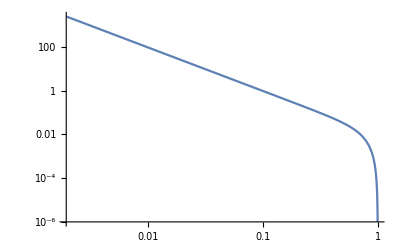

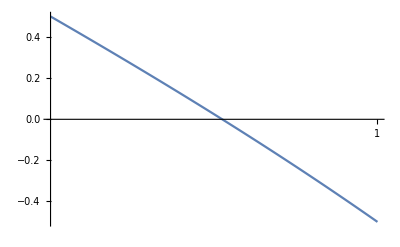

```mathematica
LogLogPlot[Dgammafunc[1,x,-1],{x,0.0,1.0}]
LogLinearPlot[Ampfunc[1,x,0.5,-1],{x,0.8,1}]
```

```mathematica
Dgamma/.cosTheta-> 0//FullSimplify
```

((h^2+1) (Mn^2-Mzprime^2)^2 (Mn^2+2 Mzprime^2))/(128 π Mn^3 Mzprime^2)

```mathematica
Collect[Amp2,{cosTheta}]
Collect[Dgamma,{cosTheta}]
```

cosTheta (h Mn √(((Mn^2-Mzprime^2)^2)/Mn^2)-(h Mn^3 √(((Mn^2-Mzprime^2)^2)/Mn^2))/(2 Mzprime^2))+(h^2 Mn^4)/(4 Mzprime^2)+(h^2 Mn^2)/4-(h^2 Mzprime^2)/2+Mn^4/(4 Mzprime^2)+Mn^2/4-Mzprime^2/2

(cosTheta (Mn^2-Mzprime^2) (4 h Mzprime^2 (Mn^2-Mzprime^2)-2 h Mn^2 (Mn^2-Mzprime^2)))/(128 π Mn^3 Mzprime^2)+((Mn^2-Mzprime^2) ((h^2+1) Mn^2 Mzprime^2+(h^2+1) Mn^4-2 (h^2+1) Mzprime^4))/(128 π Mn^3 Mzprime^2)

```mathematica
CForm[Factor[Integrate[Dgamma,{cosTheta,-1,1}]]]/.{Mzprime-> mzprime,Mn-> mh,cosTheta-> CosTheta}
```

((1 + h*h)*((mh - mzprime)*(mh - mzprime))*((mh + mzprime)*(mh + mzprime))*(mh*mh + 2*(mzprime*mzprime)))/
   (64.*(mh*mh*mh)*(mzprime*mzprime)*Pi)

```mathematica
Factor[Dgamma/.{cosTheta-> 0}]
```

((h^2+1) (Mn-Mzprime)^2 (Mn+Mzprime)^2 (Mn^2+2 Mzprime^2))/(128 π Mn^3 Mzprime^2)

## Z’ ->nu nu

```mathematica
ScalarProduct[Pp,Pp] = Mzprime^2;
ScalarProduct[P1p,P1p] = ml^2;
ScalarProduct[P2p,P2p] = ml^2;
ScalarProduct[P1p,P2p] = (-ml^2+Mzprime^2)/2;
ScalarProduct[Pp,P2p] = -Mzprime^2/2;
ScalarProduct[Pp,P1p] = -Mzprime^2/2;
```

```mathematica
m1p = -I  SpinorUBar[P2p,ml].dm[μ].SpinorV[P1p,ml]
m1Cp = ComplexConjugate[m1p]/.{μ-> μC}
```

-ⅈ ū(P2p,ml).(γ̄)^μ.v(P1p,ml)

ⅈ (φ(-OverBar[P1p],ml)).(γ̄)^μC.(φ(OverBar[P2p],ml))

```mathematica
M2p= Chop[FermionSpinSum[m1p*m1Cp]].PolarizationSum[μ,μC ,Pp]//Contract
```

(tr((γ̄·OverBar[P1p]-ml).(γ̄·OverBar[Pp]).(γ̄·OverBar[P2p]+ml).(γ̄·OverBar[Pp])))/Mzprime^2-tr((γ̄·OverBar[P1p]-ml).(γ̄)^μC.(γ̄·OverBar[P2p]+ml).(γ̄)^μC)

```mathematica
matrixelement2 =M2p/.DiracTrace->Tr/.Pair[Momentum[Pp],Momentum[Pp]]-> Mzprime^2//FullSimplify
```

10 ml^2+4 Mzprime^2

```mathematica
beta = 1/Mzprime √(Mzprime^2 - 2(2*ml^2));fluxfactor = 1/(2Mzprime);
```

```mathematica
dsigma = 1/3 epsilon^2 e^2 matrixelement2  *beta/(32 π^2)*fluxfactor//FullSimplify
```

(e^2 epsilon^2 √(Mzprime^2-4 ml^2) (5 ml^2+2 Mzprime^2))/(96 π^2 Mzprime^2)

```mathematica
dsigma *4 π/.{ml-> 0, e-> √(alpha 4π)}
```

1/3 alpha epsilon^2 √(Mzprime^2)

#### total cross section for massive leptons

```mathematica
dsigma *4 π/.{e-> √(alphaQED 4π)}//Factor//CForm
```

(alphaQED*(epsilon*epsilon)*Sqrt(-4*(ml*ml) + Mzprime*Mzprime)*(5*(ml*ml) + 2*(Mzprime*Mzprime)))/
   (6.*(Mzprime*Mzprime))

#### differential cross section

```mathematica
dsigma /.{e-> √(alphaQED 4π),π-> pi}//Factor//CForm
```

(alphaQED*(epsilon*epsilon)*Sqrt(-4*(ml*ml) + Mzprime*Mzprime)*(5*(ml*ml) + 2*(Mzprime*Mzprime))*Pi)/
   (24.*(Mzprime*Mzprime)*(pi*pi))